# WCG analysis diff 1946-1965

## TODO

共引用によるWCG結合における主要論文の寄与をどのように評価するか？

ランダムサンプリング

主要論文のみ（相手はそれ以外の論文）によるWCG結合

## Directory

```mathematica
datadir="/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/

## Program

```mathematica
largestPosition[l_List]:=Module[{largest},
largest=Max[l];
Position[l,largest]
]
```

```mathematica
selectEdgeAs["DST"][g_,src_]:=Module[{el,gth,gkeys,as},
el=EdgeList[g];
gth=GatherBy[el,#[[2]]&];
gkeys=Map[#[[1,2]]&,gth];
(*as=Inner[Rule,gkeys,gth,Association];*);
as=Association[MapThread[Rule,{gkeys,gth}]];
DeleteCases[Flatten[Map[as[#]&,src]],_Missing]
]
```

```mathematica
selectGraphAs["DST"][g_,src_]:=Module[{el,gth,gkeys,as},
el=EdgeList[g];
gth=GatherBy[el,#[[2]]&];
gkeys=Map[#[[1,2]]&,gth];
(*as=Inner[Rule,gkeys,gth,Association];*);
as=Association[MapThread[Rule,{gkeys,gth}]];
DeleteCases[Flatten[Map[as[#]&,src]],_Missing]//Graph
]
```

```mathematica
selectGraphAs["SRC"][g_,src_]:=Module[{el,gth,gkeys,as},
el=EdgeList[g];
gth=GatherBy[el,#[[1]]&];
gkeys=Map[#[[1,1]]&,gth];
(*as=Inner[Rule,gkeys,gth,Association]*);
as=Association[MapThread[Rule,{gkeys,gth}]];
DeleteCases[Flatten[Map[as[#]&,src]],_Missing]//Graph
]
```

```mathematica
selectEdgeAs["SRC"][g_,src_]:=Module[{el,gth,gkeys,as},
el=EdgeList[g];
gth=GatherBy[el,#[[1]]&];
gkeys=Map[#[[1,1]]&,gth];
(*as=Inner[Rule,gkeys,gth,Association]*);
as=Association[MapThread[Rule,{gkeys,gth}]];
DeleteCases[Flatten[Map[as[#]&,src]],_Missing]
]
```

## Basic information

上位1%被引用論文 {citingPMID(代表) -> citedPMID, count}

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/top1perc-cited-artByyear.save"];
```

```mathematica
Do[citedPMIDTop1perc[n]=Map[#[[1,2]]&,citedArtlistTop1perc[n]],
{n,1950,2020,5}]
```

## Previous : WCG 1946 - 1960

### Data

```mathematica
previousG=1960
```

1960

Graph

```mathematica
file[previousG]=datadir<>"WCG_1946-"<>ToString[previousG]<>".wl"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/WCG_1946-1960.wl

前世代WCG数*

```mathematica
(WCGlist[previousG]=Get[file[previousG]])//Length
```

4624

WCGをVertexListにする：

```mathematica
(WCGlistV[previousG]=Map[VertexList,WCGlist[previousG]])//Length
```

4624

Vertex名(PMID)からそのVertexがどのWCGに含まれるかそのpositionを返す。

```mathematica
PMIDtoWCGPos[previousG]=Association[Flatten[MapIndexed[Apply[Outer,{Rule,#1,#2}]&,WCGlistV[previousG]]]];
```

```mathematica
largestWCGPos[previousG]=Flatten[largestPosition[Map[VertexCount,WCGlist[previousG]]]]
```

{1}

```mathematica
WCGlargest[previousG]=WCGlist[previousG][[1]];
```

Nodes

```mathematica
(WCGNodes[previousG]=Map[VertexList,WCGlist[previousG]])//Length
```

4624

Edges

```mathematica
(WCGEdges[previousG]=Map[EdgeList,WCGlist[previousG]])//Length
```

4624

Global Graph

```mathematica
GlobalGraph[previousG]=Graph[Flatten[WCGEdges[previousG]]];
```

```mathematica
(*GlobalEdge[previousG]=EdgeList[GlobalGraph[previousG]];*)
```

## Current : WCG 1946 - 1965

### Data

```mathematica
currentG=1965
```

1965

Graph

```mathematica
file[currentG]=datadir<>"WCG_1946-"<>ToString[currentG]<>".wl"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/WCG_1946-1965.wl

```mathematica
(WCGlist[currentG]=Get[file[currentG]])//Length
```

5729

WCGをVertexListにする：

```mathematica
(WCGlistV[currentG]=Map[VertexList,WCGlist[currentG]])//Length
```

5729

Vertex名(PMID)からそのVertexがどのWCGに含まれるかそのpositionを返す。

```mathematica
PMIDtoWCGPos[currentG]=Association[Flatten[MapIndexed[Apply[Outer,{Rule,#1,#2}]&,WCGlistV[currentG]]]];
```

```mathematica
largestWCGPos[currentG]=Flatten[largestPosition[Map[VertexCount,WCGlist[currentG]]]]
```

{1}

```mathematica
WCGlargest[currentG]=WCGlist[currentG][[1]];
```

Nodes

```mathematica
(WCGNodes[currentG]=Map[VertexList,WCGlist[currentG]])//Length
```

5729

Edges

```mathematica
(WCGEdges[currentG]=Map[EdgeList,WCGlist[currentG]])//Length
```

5729

Global Graph

```mathematica
(*AbsoluteTiming[tmp=GlobalGraph[currentG]=Graph[Flatten[WCGEdges[currentG]]];]*)
```

```mathematica
AbsoluteTiming[GlobalGraph[currentG]=Graph[Apply[Join,WCGEdges[currentG]]];]
```

{0.491274,Null}

```mathematica
(*GlobalEdge[currentG]=EdgeList[GlobalGraph[currentG]];*)
```

## Diff : 1946-1960 < 1946-1965

A. 新規に発生した引用*

```mathematica
(WCGtotaledgeDiff[previousG,currentG]=Complement[Flatten[Map[EdgeList,WCGlist[currentG]]],Flatten[Map[EdgeList,WCGlist[previousG]]]])//Length
```

445022

B. 新規に発生した引用関係からSrc/Dstを混ぜてVertexListをつくる

```mathematica
(WCGtotalnodeDiffU[previousG,currentG]=Union[Flatten[Apply[List,WCGtotaledgeDiff[previousG,currentG],Infinity]]])//Length
```

236933

B-1. 上記VertexListより前年代のVertexでもあるものを選択（グラフを拡張するキーとなる存在:コネクション論文）

```mathematica
(WCGtotalnodeIS[previousG,currentG]=Intersection[Flatten[WCGNodes[previousG]],WCGtotalnodeDiffU[previousG,currentG]])//Length
```

79951

B-2. 上記Vertexに含まれるtop1%論文（コネクション論文かつtop1%論文）-> citedPMIDTop1percCon

```mathematica
citedPMIDTop1percCon[previousG]=Intersection[citedPMIDTop1perc[previousG],WCGtotalnodeIS[previousG,currentG]]
```

{12989928,12991232,12991237,12996882,13069686,13124776,13130792,13186838,13319380,14381428,14803635,14822727,14862161,14873923,14898516,14907661,14907713,14915960,14927794,15392854,15395398,15395569,15398090,15398551,15404816,15410483,15421999,15436457,16694480,16695228,16695286,16695568,16745305,16746620,16747230,16747508,16747652,16747784,16747948,16748273,16748381,16991506,16991878,16994401,17247100,18128147}

B-3. 新規に発生した引用のうち主要論文に対する引用*

:まずAssociationを作成:

```mathematica
WCGtotaledgeDiffGatherDSTAs=Association[Map[#[[1,2]]->#&,GatherBy[WCGtotaledgeDiff[previousG,currentG],#[[2]]&]]];
```

:AssociationをMap:

```mathematica
(fconEdgediff[currentG]=Map[WCGtotaledgeDiffGatherDSTAs,citedPMIDTop1percCon[previousG]]//Flatten)//Length
```

2835

## WCG connection of all of previous part

A-1. 新規に発生した引用関係により結合が発生した前世代WCG {WCG ID, count} (すべてが結合されたわけではない)*

```mathematica
newConnectedWCGcount[currentG]=(previousWCGfconPartAll[currentG]=Cases[Map[PMIDtoWCGPos[previousG],WCGtotalnodeIS[previousG,currentG]],_Integer]//Tally)//Length
```

1297

## WCG elongation matrix : 1946-1960 < 1946-1965

Current WCGのPMIDより、{previous-WCG-ID : current-WCG-ID}のペアを作成する。
Current WCGのPMID（デスティネーション）を渡すと前世代WCGのID（位置）を返す関数を作成する。

```mathematica
aspv=Association[Flatten[Table[Map[#->n&,VertexList[WCGlist[previousG][[n]]]],{n,Length[WCGlist[previousG]]}]]];
```

```mathematica
(cedList=Map[Map[#[[2]]&,EdgeList[#]]&,WCGlist[currentG]])//Length
```

7020

```mathematica
Timing[(elMat[currentG]=DeleteCases[Map[Map[aspv[#]&,#]&,cedList],_Missing,{2}])//Length]
```

{1.2188,7020}

```mathematica
Save[datadir<>"elongationMat.save",elMat]
```

## WCG elongation connection : 1946-1960 < 1946-1965

A-2. 新規に発生した引用関係に対して前世代の引用先がどのWCGに属するか(Missingあり <- 落としている) {“PMID” -> WCG ID}

```mathematica
(WCGtotaledgeDiffEff[previousG,currentG,"previous WCG ID"]=Cases[  Map[#[[1]]->PMIDtoWCGPos[previousG][#[[2]]]&,WCGtotaledgeDiff[previousG,currentG]]  ,x_/;Head[x[[2]]]==Integer])//Length
```

212780

ギャザー.ユニーク化

```mathematica
(WCGconUnion[previousG,currentG,"previous WCG ID"]=Map[Union,  GatherBy[WCGtotaledgeDiffEff[previousG,currentG,"previous WCG ID"],#[[1]]&]  ])//Length
```

36973

A-3. 新規に発生した引用関係により異なる前世代WCGを結合する論文（ユニーク化）*

```mathematica
newMetaconnectedcount[currentG]=(WCGelongationconUnion[previousG,currentG,"previous WCG ID"]=Cases[WCGconUnion[previousG,currentG,"previous WCG ID"],x_/;Length[x]>1])//Length
```

1717

A-4. 新規に結合された前世代WCG（全てが統合された訳ではない）*

```mathematica
newMetaconnectedWCGcount[currentG]=(WCGnewconnected[previousG,currentG]=Union[Map[#[[2]]&,Flatten[WCGelongationconUnion[previousG,currentG,"previous WCG ID"]]]])//Length
```

1070

## Visualization (top 1% article part)

### グラフの主要接続部分のパターン定義

主要接続部分とはグラフ差分のうちで主要論文が関与する部分。本研究の流れではフォワードコネクション （主要論文の被引用） を使うのが妥当か。

コネクション論文かつ上位1%論文付近のネットワーク（当年代）

:フォワードコネクション（上位1%コネクション論文が引用される;年代を進める）previous

```mathematica
citedPMIDTop1percCon[previousG]
```

{12989928,12991232,12991237,12996882,13069686,13124776,13130792,13186838,13319380,14381428,14803635,14822727,14862161,14873923,14898516,14907661,14907713,14915960,14927794,15392854,15395398,15395569,15398090,15398551,15404816,15410483,15421999,15436457,16694480,16695228,16695286,16695568,16745305,16746620,16747230,16747508,16747652,16747784,16747948,16748273,16748381,16991506,16991878,16994401,17247100,18128147}

### current: 1965におけるグラフの接続部分

#### *フォワード

関数のSubgraph[]と同じ結果が欲しければ、結果のvertexlistをキーにしてSubgraph[]する。（今回不要なはず）

```mathematica
fconGraph[currentG]=selectGraphAs["DST"][GlobalGraph[currentG],citedPMIDTop1percCon[previousG]];
```

```mathematica
vl=VertexList[fconGraph[currentG]];
```

```mathematica
(fconEdgelist[currentG]=EdgeList[fconGraph[currentG]])//Length
```

7571

```mathematica
(fconNodelist[currentG]=VertexList[fconGraph[currentG]])//Length
```

6290

#### *バックワード

```mathematica
(fconEdgeSRC[currentG]=Union[Map[#[[1]]&,fconEdgelist[currentG]]])//Length
```

6253

```mathematica
AbsoluteTiming[bconGraph[currentG]=selectGraphAs["SRC"][GlobalGraph[currentG],fconEdgeSRC[currentG]]]
```

{1.21616,}

```mathematica
(bconNodelist[currentG]=VertexList[bconGraph[currentG]])//Length
```

47206

top1%論文による前世代グラフのWCG接続

```mathematica
previousWCGfconPartTop1perc[currentG]=Cases[Map[PMIDtoWCGPos[previousG],bconNodelist[currentG]],_Integer]//Tally//Sort
```

{{1,32517},{9,1},{100,3},{156,1},{222,1},{224,2},{384,1},{393,1},{458,1},{625,1},{643,1},{705,1},{1176,1},{1189,1},{1202,1},{1212,1},{1234,1},{1263,1},{1538,1},{1546,1},{1598,1},{1652,1},{1676,1},{1738,1},{1746,1},{1825,1},{1955,1},{2167,1},{2259,1},{2544,1},{2655,2},{2700,1},{2734,1},{2748,1},{2788,1},{3009,1},{3024,1},{3057,1},{3170,1},{3343,1},{3542,2},{3590,1},{3641,2},{3664,2},{4105,1},{4609,1}}

```mathematica
(*Export["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/connectionpartGraph_"<>ToString[previousG]<>"-"<>ToString[currentG]<>".wl",bconGraph[currentG]]*)
```

### 上位1%論文による1960と1965のグラフの差分

#### *フォワード : 差分

```mathematica
vstyle=Map[#->Orange&,citedPMIDTop1percCon[previousG]]
```

{12989928→RGBColor[1, 0.5, 0],12991232→RGBColor[1, 0.5, 0],12991237→RGBColor[1, 0.5, 0],12996882→RGBColor[1, 0.5, 0],13069686→RGBColor[1, 0.5, 0],13124776→RGBColor[1, 0.5, 0],13130792→RGBColor[1, 0.5, 0],13186838→RGBColor[1, 0.5, 0],13319380→RGBColor[1, 0.5, 0],14381428→RGBColor[1, 0.5, 0],14803635→RGBColor[1, 0.5, 0],14822727→RGBColor[1, 0.5, 0],14862161→RGBColor[1, 0.5, 0],14873923→RGBColor[1, 0.5, 0],14898516→RGBColor[1, 0.5, 0],14907661→RGBColor[1, 0.5, 0],14907713→RGBColor[1, 0.5, 0],14915960→RGBColor[1, 0.5, 0],14927794→RGBColor[1, 0.5, 0],15392854→RGBColor[1, 0.5, 0],15395398→RGBColor[1, 0.5, 0],15395569→RGBColor[1, 0.5, 0],15398090→RGBColor[1, 0.5, 0],15398551→RGBColor[1, 0.5, 0],15404816→RGBColor[1, 0.5, 0],15410483→RGBColor[1, 0.5, 0],15421999→RGBColor[1, 0.5, 0],15436457→RGBColor[1, 0.5, 0],16694480→RGBColor[1, 0.5, 0],16695228→RGBColor[1, 0.5, 0],16695286→RGBColor[1, 0.5, 0],16695568→RGBColor[1, 0.5, 0],16745305→RGBColor[1, 0.5, 0],16746620→RGBColor[1, 0.5, 0],16747230→RGBColor[1, 0.5, 0],16747508→RGBColor[1, 0.5, 0],16747652→RGBColor[1, 0.5, 0],16747784→RGBColor[1, 0.5, 0],16747948→RGBColor[1, 0.5, 0],16748273→RGBColor[1, 0.5, 0],16748381→RGBColor[1, 0.5, 0],16991506→RGBColor[1, 0.5, 0],16991878→RGBColor[1, 0.5, 0],16994401→RGBColor[1, 0.5, 0],17247100→RGBColor[1, 0.5, 0],18128147→RGBColor[1, 0.5, 0]}

```mathematica
vsize=Map[#->16&,citedPMIDTop1percCon[previousG]]
```

{12989928→16,12991232→16,12991237→16,12996882→16,13069686→16,13124776→16,13130792→16,13186838→16,13319380→16,14381428→16,14803635→16,14822727→16,14862161→16,14873923→16,14898516→16,14907661→16,14907713→16,14915960→16,14927794→16,15392854→16,15395398→16,15395569→16,15398090→16,15398551→16,15404816→16,15410483→16,15421999→16,15436457→16,16694480→16,16695228→16,16695286→16,16695568→16,16745305→16,16746620→16,16747230→16,16747508→16,16747652→16,16747784→16,16747948→16,16748273→16,16748381→16,16991506→16,16991878→16,16994401→16,17247100→16,18128147→16}

新しく増えた引用関係（currentのconエッジ - previousのconエッジ）のハイライト

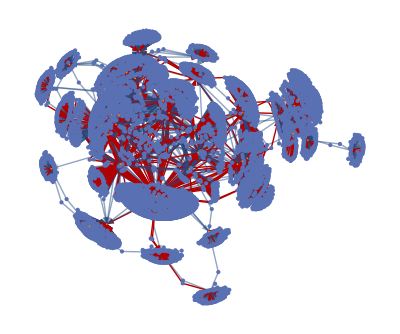

```mathematica
fconGraphD[currentG]=Graph[fconGraph[currentG],GraphHighlight->Flatten[{fconEdgediff[currentG]}],VertexStyle->vstyle,VertexSize->vsize]
```

可視化対象の構造だけはExportしておく。

```mathematica
(*Export[datadir<>"gdiffF_"<>ToString[currentG]<>".wl",fconGraphD[currentG]]*)
```